```mathematica
SetSystemOptions["ParallelOptions"->{"ParallelThreadNumber"->20,"MKLThreadNumber"->20}]
KimuraEig[i_]:=1/2*i*(i+1);
(*The integrand of all the time integrals*)
integrand[k_]:=Exp[Sum[( KimuraEig[q[i+1]] - KimuraEig[q[i]] - (2^(1+r[i])* Ne * VG / W))s[i],{i,1,k}]];
(*The limits of the time integrals*)
sLimits[k_]:= Join[{{s[k],0,t}},Reverse[Table[{s[j],0,s[j+1]},{j,1,k-1}]]];
(*Define the limits of the k fold sum over the j_i s *)
rLimits[k_] := Table[{r[i],0,1},{i,1,k}];
(*Define the limits of the k+1 fold infinite sums. Truncating after n_ terms*)
qLimits[k_, n_ ] := Join[{{q[1],1,n}},Table[{q[j],q[j-1]-2,q[j-1]+2,1},{j,2,k+1}]];
```

ParallelOptions→{AbortPause→2.,BusyWait→0.01,MathLinkTimeout→15.,MKLThreadNumber→20,ParallelThreadNumber→20,RecoveryMode→Retry,RelaunchFailedKernels→True,VectorParallelLengthThresholds→{8192,8192,8192,8192,8192},VectorVendorLengthThresholds→{128,32,32}}

```mathematica
computeInts[k_] := Integrate[integrand[k], Evaluate[Sequence@@sLimits[k]]]
```

```mathematica
(*These functions are to compute the Gegenbauer integrals*)
(*The normalizations for the Gegenbauer polynomials*)
gegenbauerNorm[i_,λ_:3/2] := π*2^(1-2*λ)*Gamma[i+2*λ]/(Factorial[i]*(i+λ)*Gamma[λ]^2);
(*Define Int_{0^1}x^2(1-x)^(1+j)C_{i-1}^{(3/2)}(1-2*x)C_{j-1}^{(3/2)}(1-2*x)dx*)
f[0,0]=1;
f[a_,b_]:=a^b
gegenbauerInt[a_,b_,r_]:=KroneckerDelta[a,b]* gegenbauerNorm[a] - 
(f[(1/(3+2a) * 
((a+1)*KroneckerDelta[a,b-1]*gegenbauerNorm[a+1]+
(a+2)*KroneckerDelta[a,b+1]*gegenbauerNorm[a-1])),(1-r) ] * (*3rdd to last partenthesis on this line was missing. check if this fixed*)
f[(1/((2*a+3)*(2*b+3))*
((a+1)*(b+1)*KroneckerDelta[a,b]*gegenbauerNorm[a+1]+
(a+1)*(b+2)*KroneckerDelta[a,b-2]*gegenbauerNorm[a+1]+
(a+2)*(b+1)*KroneckerDelta[a,b+2]*gegenbauerNorm[a-1]+
(a+2)*(b+2)*KroneckerDelta[a,b]*gegenbauerNorm[a-1])),r]);
```

```mathematica
(*Functions to compute the path integral to order k*)
(*Define the coefficients from Kimura's solution*)
kimuraCoefficient[i_]:= If[i>0,4*(2*i+1)/(i*(i+1)),0];
(*Kimura's transition density*)
(*TODO get rid of the default*)
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
(*Compute the path integral at order k*)
pathInt[x_,y_,t_,k_,n_, Ne_, α_, Λ_, W_,VG_]:= Module[{qlims, rlims, lims, tInts,pm},
(*myInds = Table[{i[j],1,n},{j,1,k+1}];*)
qlims = qLimits[k,n];
rlims = rLimits[k];
lims = Join[qlims,rlims];
tInts = computeInts[k];
(*pm=partitionMap[k];*)
x*(1-x)*ParallelSum[If[Negative@Min@Table[q[j],{j,1,k+1}],0,
Product[kimuraCoefficient[q[j]],{j,1,k+1}]*
Exp[-KimuraEig[q[k+1]]*t]*
GegenbauerC[q[1]-1,3/2,1-2*x]*
GegenbauerC[q[k+1]-1,3/2,1-2*y]*
Product[(2VG)^(1-r[j]) (- α Λ)^r[j] 2^(-(4+r[j]))*gegenbauerInt[q[j]-1,q[j+1]-1, r[j]],{j,1,k}]*
tInts],Evaluate[Sequence@@lims]]];
```

```mathematica
Get["o1through4.m"]
```

```mathematica
(*TODO find out if we need to do the find Equiv thing or not. It'd make a difference for VG = 0 but only if that is declared prior to the integrand being calculated*)
```

```mathematica
new[0] = Kimura[x,y,t,10];
```

```mathematica
o[0]/.{x->.2,y->.4,t->.2}
new[0]/.{x->.2,y->.4,t->.2}
new[0] == o[0] //FullSimplify
```

0.937609

0.937609

True

```mathematica
genVar
```

0.00705098

```mathematica
new[1] = Table[pathInt[x,y,t,k,10, Ne, α, Λ, W,VG],
{k,{1}},{VG,{0.007050979}}, {Ne, {500}}, {W,{1}}];
```

```mathematica
2*0.0011555272914038413
```

0.00231105

```mathematica
new[1]
```

{{{{(1-x) x (0.+0.003 ⅇ^-t (2.-2. ⅇ^(-7.05098 t))-0.00233709 ⅇ^-t (2.-2. ⅇ^(-9.05098 t)) (1-2 x)+0.00116667 ⅇ^(-6 t) (2.-2. ⅇ^(-7.05098 t)) (-3/2+15/2 (1-2 x)^2) (-3/2+15/2 (1-2 y)^2)-0.000319021 ⅇ^(-6 t) (2.-2. ⅇ^(-11.051 t)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-3/2+15/2 (1-2 y)^2)-0.00348112 ⅇ^(-6 t) (2.-2. ⅇ^(-4.05098 t)) (1-2 x) (-3/2+15/2 (1-2 y)^2)-0.00115553 ⅇ^(-10 t) (2.-2. ⅇ^(-3.05098 t)) (-3/2+15/2 (1-2 x)^2) (-15/2 (1-2 y)+35/2 (1-2 y)^3)+0.0009 ⅇ^(-10 t) (2.-2. ⅇ^(-7.05098 t)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-15/2 (1-2 y)+35/2 (1-2 y)^3)-0.000234038 ⅇ^(-10 t) (2.-2. ⅇ^(-12.051 t)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-15/2 (1-2 y)+35/2 (1-2 y)^3)-0.00137514 ⅇ^(-15 t) (2.-2. ⅇ^(-2.05098 t)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4)+0.000733333 ⅇ^(-15 t) (2.-2. ⅇ^(-7.05098 t)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4)-0.000180088 ⅇ^(-15 t) (2.-2. ⅇ^(-13.051 t)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4)-0.00223632 ⅇ^(-21 t) (2.-2. ⅇ^(-1.05098 t)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5)+0.000619048 ⅇ^(-21 t) (2.-2. ⅇ^(-7.05098 t)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5)-0.000143375 ⅇ^(-21 t) (2.-2. ⅇ^(-14.051 t)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5)-0.0395176 ⅇ^(-28 t) (2.-2. ⅇ^(-0.050979 t)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6)+0.000535714 ⅇ^(-28 t) (2.-2. ⅇ^(-7.05098 t)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6)-0.000117118 ⅇ^(-28 t) (2.-2. ⅇ^(-15.051 t)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6)+0.00185743 ⅇ^(-36 t) (2.-2. ⅇ^(0.949021 t)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)+0.000472222 ⅇ^(-36 t) (2.-2. ⅇ^(-7.05098 t)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)-0.0000976192 ⅇ^(-36 t) (2.-2. ⅇ^(-16.051 t)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)+0.000803934 ⅇ^(-45 t) (2.-2. ⅇ^(1.94902 t)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8)+0.000422222 ⅇ^(-45 t) (2.-2. ⅇ^(-7.05098 t)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8)-0.0000827047 ⅇ^(-45 t) (2.-2. ⅇ^(-17.051 t)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8)+0.000478191 ⅇ^(-55 t) (2.-2. ⅇ^(2.94902 t)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9)+0.000381818 ⅇ^(-55 t) (2.-2. ⅇ^(-7.05098 t)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9)+0.000324636 ⅇ^(-66 t) (2.-2. ⅇ^(3.94902 t)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10)-0.00418789 ⅇ^(-3 t) (2.-2. ⅇ^(-5.05098 t)) (1-2 y)-0.00140304 ⅇ^(-3 t) (2.-2. ⅇ^(-10.051 t)) (-3/2+15/2 (1-2 x)^2) (1-2 y)+0.015 ⅇ^(-3 t) (2.-2. ⅇ^(-7.05098 t)) (1-2 x) (1-2 y)-0.0425473 ⅇ^-t (2.-2. ⅇ^(-14.102 t)) α Λ+0.00523507 ⅇ^-t (2.-2. ⅇ^(-19.102 t)) (-3/2+15/2 (1-2 x)^2) α Λ+0.0109866 ⅇ^(-6 t) (2.-2. ⅇ^(-9.10196 t)) (-3/2+15/2 (1-2 y)^2) α Λ-0.0110308 ⅇ^(-6 t) (2.-2. ⅇ^(-14.102 t)) (-3/2+15/2 (1-2 x)^2) (-3/2+15/2 (1-2 y)^2) α Λ+0.0024048 ⅇ^(-6 t) (2.-2. ⅇ^(-23.102 t)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-3/2+15/2 (1-2 y)^2) α Λ-0.00828843 ⅇ^(-10 t) (2.-2. ⅇ^(-14.102 t)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ+0.0018108 ⅇ^(-10 t) (2.-2. ⅇ^(-25.102 t)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ+0.0301728 ⅇ^(-10 t) (2.-2. ⅇ^(-7.10196 t)) (1-2 x) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ+0.0108891 ⅇ^(-15 t) (2.-2. ⅇ^(-5.10196 t)) (-3/2+15/2 (1-2 x)^2) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ-0.00666695 ⅇ^(-15 t) (2.-2. ⅇ^(-14.102 t)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ+0.00141914 ⅇ^(-15 t) (2.-2. ⅇ^(-27.102 t)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ+0.0146535 ⅇ^(-21 t) (2.-2. ⅇ^(-3.10196 t)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ-0.00558702 ⅇ^(-21 t) (2.-2. ⅇ^(-14.102 t)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ+0.0011454 ⅇ^(-21 t) (2.-2. ⅇ^(-29.102 t)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ+0.0349029 ⅇ^(-28 t) (2.-2. ⅇ^(-1.10196 t)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ-0.00481304 ⅇ^(-28 t) (2.-2. ⅇ^(-14.102 t)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ+0.000945656 ⅇ^(-28 t) (2.-2. ⅇ^(-31.102 t)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ-0.0371178 ⅇ^(-36 t) (2.-2. ⅇ^(0.898042 t)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ-0.00422985 ⅇ^(-36 t) (2.-2. ⅇ^(-14.102 t)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ+0.000794992 ⅇ^(-36 t) (2.-2. ⅇ^(-33.102 t)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ-0.0101488 ⅇ^(-45 t) (2.-2. ⅇ^(2.89804 t)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α Λ-0.00377404 ⅇ^(-45 t) (2.-2. ⅇ^(-14.102 t)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α Λ-0.00537272 ⅇ^(-55 t) (2.-2. ⅇ^(4.89804 t)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α Λ-0.00340768 ⅇ^(-55 t) (2.-2. ⅇ^(-14.102 t)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α Λ-0.00345164 ⅇ^(-66 t) (2.-2. ⅇ^(6.89804 t)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) α Λ-0.00244314 ⅇ^(-78 t) (2.-2. ⅇ^(8.89804 t)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-9009/256 (1-2 y)+225225/256 (1-2 y)^3-765765/128 (1-2 y)^5+2078505/128 (1-2 y)^7-4849845/256 (1-2 y)^9+2028117/256 (1-2 y)^11) α Λ+0.0101548 ⅇ^(-3 t) (2.-2. ⅇ^(-21.102 t)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (1-2 y) α Λ-0.151955 ⅇ^(-3 t) (2.-2. ⅇ^(-14.102 t)) (1-2 x) (1-2 y) α Λ)}}}}

```mathematica
N[3/500  ]
```

0.006

```mathematica
pew[1]=pathInt[x,y,t,1,10, Ne, α, Λ, W,VG];
```

```mathematica
pew[1]
```

```mathematica
new[1]
```

(1-x) x (0.+(0.0211529 ⅇ^-t (1-ⅇ^(-(2 Ne t VG)/W)) W)/(Ne VG)-(0.0846117 ⅇ^-t (1-ⅇ^(-1/2 t (4+(4 Ne VG)/W))) W (1-2 x))/(4 Ne VG+4 W)+(0.00822614 ⅇ^(-6 t) (1-ⅇ^(-(2 Ne t VG)/W)) W (-3/2+15/2 (1-2 x)^2) (-3/2+15/2 (1-2 y)^2))/(Ne VG)-1/(4 Ne VG+8 W)0.014102 ⅇ^(-6 t) (1-ⅇ^(-1/2 t (8+(4 Ne VG)/W))) W (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-3/2+15/2 (1-2 y)^2)-(0.0564078 ⅇ^(-6 t) (1-ⅇ^(-1/2 t (-6+(4 Ne VG)/W))) W (1-2 x) (-3/2+15/2 (1-2 y)^2))/(4 Ne VG-6 W)-1/(4 Ne VG-8 W)0.014102 ⅇ^(-10 t) (1-ⅇ^(-1/2 t (-8+(4 Ne VG)/W))) W (-3/2+15/2 (1-2 x)^2) (-15/2 (1-2 y)+35/2 (1-2 y)^3)+1/(Ne VG)0.00634588 ⅇ^(-10 t) (1-ⅇ^(-(2 Ne t VG)/W)) W (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-15/2 (1-2 y)+35/2 (1-2 y)^3)-1/(4 Ne VG+10 W)0.0112816 ⅇ^(-10 t) (1-ⅇ^(-1/2 t (10+(4 Ne VG)/W))) W (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-15/2 (1-2 y)+35/2 (1-2 y)^3)-1/(4 Ne VG-10 W)0.0112816 ⅇ^(-15 t) (1-ⅇ^(-1/2 t (-10+(4 Ne VG)/W))) W (-15/2 (1-2 x)+35/2 (1-2 x)^3) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4)+1/(Ne VG)0.00517072 ⅇ^(-15 t) (1-ⅇ^(-(2 Ne t VG)/W)) W (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4)-1/(4 Ne VG+12 W)0.00940131 ⅇ^(-15 t) (1-ⅇ^(-1/2 t (12+(4 Ne VG)/W))) W (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4)-1/(4 Ne VG-12 W)0.00940131 ⅇ^(-21 t) (1-ⅇ^(-1/2 t (-12+(4 Ne VG)/W))) W (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5)+1/(Ne VG)0.00436489 ⅇ^(-21 t) (1-ⅇ^(-(2 Ne t VG)/W)) W (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5)-1/(4 Ne VG+14 W)0.00805826 ⅇ^(-21 t) (1-ⅇ^(-1/2 t (14+(4 Ne VG)/W))) W (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5)-1/(4 Ne VG-14 W)0.00805826 ⅇ^(-28 t) (1-ⅇ^(-1/2 t (-14+(4 Ne VG)/W))) W (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6)+1/(Ne VG)0.00377731 ⅇ^(-28 t) (1-ⅇ^(-(2 Ne t VG)/W)) W (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6)-1/(4 Ne VG+16 W)0.00705098 ⅇ^(-28 t) (1-ⅇ^(-1/2 t (16+(4 Ne VG)/W))) W (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6)-1/(4 Ne VG-16 W)0.00705098 ⅇ^(-36 t) (1-ⅇ^(-1/2 t (-16+(4 Ne VG)/W))) W (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)+1/(Ne VG)0.00332963 ⅇ^(-36 t) (1-ⅇ^(-(2 Ne t VG)/W)) W (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)-1/(4 Ne VG+18 W)0.00626754 ⅇ^(-36 t) (1-ⅇ^(-1/2 t (18+(4 Ne VG)/W))) W (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)-1/(4 Ne VG-18 W)0.00626754 ⅇ^(-45 t) (1-ⅇ^(-1/2 t (-18+(4 Ne VG)/W))) W (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8)+1/(Ne VG)0.00297708 ⅇ^(-45 t) (1-ⅇ^(-(2 Ne t VG)/W)) W (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8)-1/(4 Ne VG+20 W)0.00564078 ⅇ^(-45 t) (1-ⅇ^(-1/2 t (20+(4 Ne VG)/W))) W (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8)-1/(4 Ne VG-20 W)0.00564078 ⅇ^(-55 t) (1-ⅇ^(-1/2 t (-20+(4 Ne VG)/W))) W (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9)+1/(Ne VG)0.00269219 ⅇ^(-55 t) (1-ⅇ^(-(2 Ne t VG)/W)) W (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9)-1/(4 Ne VG-22 W)0.00512798 ⅇ^(-66 t) (1-ⅇ^(-1/2 t (-22+(4 Ne VG)/W))) W (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10)-(0.0846117 ⅇ^(-3 t) (1-ⅇ^(-1/2 t (-4+(4 Ne VG)/W))) W (1-2 y))/(4 Ne VG-4 W)-(0.0564078 ⅇ^(-3 t) (1-ⅇ^(-1/2 t (6+(4 Ne VG)/W))) W (-3/2+15/2 (1-2 x)^2) (1-2 y))/(4 Ne VG+6 W)+(0.105765 ⅇ^(-3 t) (1-ⅇ^(-(2 Ne t VG)/W)) W (1-2 x) (1-2 y))/(Ne VG)-(0.3 ⅇ^-t (1-ⅇ^(-(4 Ne t VG)/W)) W α Λ)/(Ne VG)+(0.4 ⅇ^-t (1-ⅇ^(-1/2 t (10+(8 Ne VG)/W))) W (-3/2+15/2 (1-2 x)^2) α Λ)/(8 Ne VG+10 W)+(0.4 ⅇ^(-6 t) (1-ⅇ^(-1/2 t (-10+(8 Ne VG)/W))) W (-3/2+15/2 (1-2 y)^2) α Λ)/(8 Ne VG-10 W)-1/(Ne VG)0.0777778 ⅇ^(-6 t) (1-ⅇ^(-(4 Ne t VG)/W)) W (-3/2+15/2 (1-2 x)^2) (-3/2+15/2 (1-2 y)^2) α Λ+1/(8 Ne VG+18 W)0.222222 ⅇ^(-6 t) (1-ⅇ^(-1/2 t (18+(8 Ne VG)/W))) W (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-3/2+15/2 (1-2 y)^2) α Λ-1/(Ne VG)0.0584416 ⅇ^(-10 t) (1-ⅇ^(-(4 Ne t VG)/W)) W (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ+1/(8 Ne VG+22 W)0.181818 ⅇ^(-10 t) (1-ⅇ^(-1/2 t (22+(8 Ne VG)/W))) W (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ+1/(8 Ne VG-14 W)0.857143 ⅇ^(-10 t) (1-ⅇ^(-1/2 t (-14+(8 Ne VG)/W))) W (1-2 x) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ+1/(8 Ne VG-18 W)0.222222 ⅇ^(-15 t) (1-ⅇ^(-1/2 t (-18+(8 Ne VG)/W))) W (-3/2+15/2 (1-2 x)^2) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ-1/(Ne VG)0.0470085 ⅇ^(-15 t) (1-ⅇ^(-(4 Ne t VG)/W)) W (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ+1/(8 Ne VG+26 W)0.153846 ⅇ^(-15 t) (1-ⅇ^(-1/2 t (26+(8 Ne VG)/W))) W (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ+1/(8 Ne VG-22 W)0.181818 ⅇ^(-21 t) (1-ⅇ^(-1/2 t (-22+(8 Ne VG)/W))) W (-15/2 (1-2 x)+35/2 (1-2 x)^3) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ-1/(Ne VG)0.0393939 ⅇ^(-21 t) (1-ⅇ^(-(4 Ne t VG)/W)) W (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ+1/(8 Ne VG+30 W)0.133333 ⅇ^(-21 t) (1-ⅇ^(-1/2 t (30+(8 Ne VG)/W))) W (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ+1/(8 Ne VG-26 W)0.153846 ⅇ^(-28 t) (1-ⅇ^(-1/2 t (-26+(8 Ne VG)/W))) W (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ-1/(Ne VG)0.0339367 ⅇ^(-28 t) (1-ⅇ^(-(4 Ne t VG)/W)) W (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ+1/(8 Ne VG+34 W)0.117647 ⅇ^(-28 t) (1-ⅇ^(-1/2 t (34+(8 Ne VG)/W))) W (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ+1/(8 Ne VG-30 W)0.133333 ⅇ^(-36 t) (1-ⅇ^(-1/2 t (-30+(8 Ne VG)/W))) W (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ-1/(Ne VG)0.0298246 ⅇ^(-36 t) (1-ⅇ^(-(4 Ne t VG)/W)) W (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ+1/(8 Ne VG+38 W)0.105263 ⅇ^(-36 t) (1-ⅇ^(-1/2 t (38+(8 Ne VG)/W))) W (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ+1/(8 Ne VG-34 W)0.117647 ⅇ^(-45 t) (1-ⅇ^(-1/2 t (-34+(8 Ne VG)/W))) W (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α Λ-1/(Ne VG)0.0266106 ⅇ^(-45 t) (1-ⅇ^(-(4 Ne t VG)/W)) W (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α Λ+1/(8 Ne VG-38 W)0.105263 ⅇ^(-55 t) (1-ⅇ^(-1/2 t (-38+(8 Ne VG)/W))) W (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α Λ-1/(Ne VG)0.0240275 ⅇ^(-55 t) (1-ⅇ^(-(4 Ne t VG)/W)) W (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α Λ+1/(8 Ne VG-42 W)0.0952381 ⅇ^(-66 t) (1-ⅇ^(-1/2 t (-42+(8 Ne VG)/W))) W (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) α Λ+1/(8 Ne VG-46 W)0.0869565 ⅇ^(-78 t) (1-ⅇ^(-1/2 t (-46+(8 Ne VG)/W))) W (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-9009/256 (1-2 y)+225225/256 (1-2 y)^3-765765/128 (1-2 y)^5+2078505/128 (1-2 y)^7-4849845/256 (1-2 y)^9+2028117/256 (1-2 y)^11) α Λ+1/(8 Ne VG+14 W)0.857143 ⅇ^(-3 t) (1-ⅇ^(-1/2 t (14+(8 Ne VG)/W))) W (-15/2 (1-2 x)+35/2 (1-2 x)^3) (1-2 y) α Λ-(1.07143 ⅇ^(-3 t) (1-ⅇ^(-(4 Ne t VG)/W)) W (1-2 x) (1-2 y) α Λ)/(Ne VG))

```mathematica
o[1]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
new[1]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
new[1] == o[1] //FullSimplify
```

0.000376652

0.000376652

$Aborted

```mathematica
new[2] = pathInt[x,y,t,2,10, Ne, α, Λ, W,VG];
```

```mathematica
o[2]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
new[2]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-801.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

7.57994×10^-8

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-801.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

7.57994×10^-8

```mathematica
o[2]
```

```mathematica
new[2]
```

```mathematica
new[3] = pathInt[x,y,t,3,10, Ne, α, Λ, W,VG];
```

```mathematica
SetPrecision[SetAccuracy[o[3],100],100]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
SetPrecision[SetAccuracy[new[3],100],100]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

General::munfl: 1/(«122»)^800. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

9.9027×10^-12

General::munfl: 1/(«122»)^800. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(«122»)^801. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.01963×10^-11

```mathematica
new[4] = pathInt[x,y,t,4,10, Ne, α, Λ, W,VG];
```

```mathematica
SetPrecision[SetAccuracy[o[4],100],100]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
SetPrecision[SetAccuracy[new[4],100],100]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

General::munfl: 1/(«122»)^800. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-5.16496×10^-14

General::munfl: 1/(«122»)^800. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.03412×10^-15

```mathematica
new[5] = pathInt[x,y,t,5,10, Ne, α, Λ, W,VG]
```

```mathematica
SetPrecision[SetAccuracy[new[5],1000],1000]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

General::munfl: 1/(«1029»)^1000. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(«1029»)^800. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(«1029»)^1000. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

8.34262×10^-20

```mathematica
Accuracy[8.342624600834647*^-20]
```

35.0333

```mathematica
Precision[8.342624600834647*^-20]
```

MachinePrecision

```mathematica
N[MachinePrecision]
```

15.9546

```mathematica
SetPrecision[SetAccuracy[new[5]/.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1},1000],1000]
```

General::munfl: Exp[-1000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

8.3426246008352376968457051337906123635473482806631877715941580930802956572733819484710693359375×10^-20

```mathematica
Precision[8.3426246008352376968457051337906123635473482806631877715941580930802956572733819484710693359375`1000.*^-20]
```

1000.

```mathematica
Accuracy[8.3426246008352376968457051337906123635473482806631877715941580930802956572733819484710693359375`1000.*^-20]
```

1019.08

```mathematica
new[6] = pathInt[x,y,t,6,10, Ne, α, Λ, W,VG]
```

```mathematica
(*Save["new1through5Sequential.m",new]*)
Get["new1through5Sequential.m"]
```

```mathematica
For[j=0, j ≤5, j++,
Print[ SetPrecision[SetAccuracy[o[j] /.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1},100],100]];
Print[SetPrecision[SetAccuracy[new[j] /.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1},100],100]]
]
```

0.93760851066392769670443385621183551847934722900390625

0.93760851066392769670443385621183551847934722900390625

0.0003766518686785827701828111013782063309918157756328582763671875

0.0003766518686785827701828111013782063309918157756328582763671875

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-801.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

7.57994132690562754696428360290383352548815310001373291015625×10^-8

7.57994132690562754696428360290383352548815310001373291015625×10^-8

9.9027025157204338826781040533195452253700796774182890658266842365264892578125×10^-12

1.019626188970965012867735204301600205299693779892322709201835095882415771484375×10^-11

-5.16496141883935395654349174677171995529183397277694922422597301192581653594970703125×10^-14

1.034123514961921572952810212025080084506604830886511425802609664970077574253082275390625×10^-15

o[5.]

8.3426246008352376968457051337906123635473482806631877715941580930802956572733819484710693359375×10^-20

```mathematica
For[j=0, j ≤5, j++,
Print[(2 Ne^2 α Λ / W^2)^j * o[j] /.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->.0113452342}];
Print[(2 Ne^2 α Λ / W^2)^j * new[j] /.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->.0113452342}]
]
```

0.937609

0.937609

1.02765

1.02765

0.587626

0.587626

0.233071

0.233071

0.0719537

0.0719537

9.76563×10^16 o[5]

0.0183946

```mathematica
(*newversion = (2 Ne^2 α Λ / W^2)^2 * o[2]*)
```

```mathematica
(2 Ne^2 α Λ / W^2)^3 * o[3] /.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.15473

```mathematica
NumberForm[0.15472972680813177,16]
```

0.1547297268081318

```mathematica
(*DumpSave["newversion.mx",newversion]*)
For[k = 0, k ≤5,k++,
approx[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

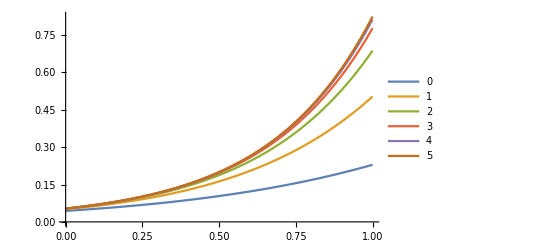

```mathematica
Plot[Evaluate[Table[approx[k]/. {x->0.5, t->1,Ne->500,α->0.005, Λ -> 1, W->1, VG->.001111},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

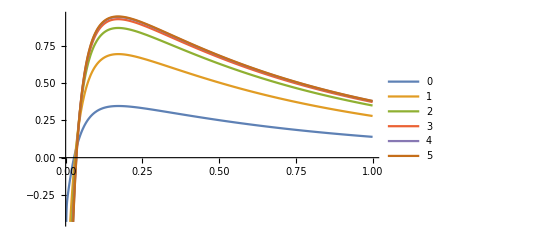

```mathematica
Plot[Evaluate[Table[approx[k]/. {x->0.2, y->0.4,Ne->500,α->0.005, Λ -> 1, W->1, VG->1},{k,0, 5}]],{t,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

```mathematica
Plot[Evaluate[approx[5]/. {x->0.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}]{y,0,1},{t,0,0.1}]
```

$Aborted

```mathematica
GaussianApprox[y_,x_,t_, Ne_,α_, Λ_, W_] := (2 π x (1-x) t)^(-1/2) Exp[-(y-(x+2Ne α Λ x (1-x) t / W))^2 / (2 x (1-x) t)]
```

```mathematica
approx[5] /. {x->0.2, t->0.1,Ne->500,α->0.005, Λ -> 1, W->1, VG->1, y ->0.4}
```

General::munfl: (9.85968×10^-305)/4480 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.93443×10^-308)/125000000 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.852542

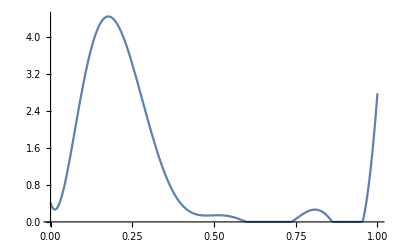

```mathematica
Plot[Evaluate[Max[(approx[5]/. {x->0.2, t->0.05,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}), 0]],{y,0,1}]
```

```mathematica
NIntegrate[(approx[5] /.{x->0.2, t->0.01,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}), {y,0,1}]
```

1.16688

```mathematica
(2 Ne^2 α Λ / W^2)^4/.{Ne->500,α->0.005, Λ -> 1, W->1}
```

3.90625×10^13

```mathematica
o[4] /.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-5.16496×10^-14

```mathematica
(2 Ne^2 α Λ / W^2)^4 *o[4] /.{x->.2,y->.4,t->.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-2.01756

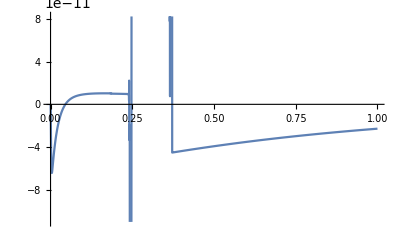

```mathematica
Plot[Evaluate[o[3]/.{x->.2,y->.4,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}], {t,0,1}]
```

```mathematica
Max[Last/@Level[Cases[%,_Line,Infinity],{-2}]]
```

8.21821×10^-11

```mathematica
pade = PadeApproximant[approx/.γ^2->g,{g,0,2}]/.g->γ^2;
```

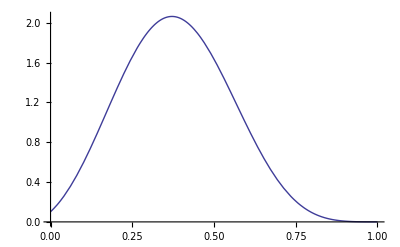

```mathematica
Plot[pade/.{x->.2,t->.1,γ->10},{y,0,1}]
```

```mathematica
vals10 = Table[approx/.{x->.2,t->.1,γ->5},{y,0,1,.05}]
```

{0.364043,0.942617,1.56848,2.1083,2.46219,2.58194,2.47292,2.1829,1.78335,1.34942,0.943708,0.606975,0.356141,0.188323,0.0881546,0.0355679,0.0118655,0.00305193,0.00052951,0.0000446591,1.4838×10^-7}

```mathematica
Export["~/Desktop/testMathematica.txt",vals10]
```

~/Desktop/testMathematica.txt

```mathematica
mass = Table[NIntegrate[approx/.{x->.2,t->.1},{y,0,1}],{γ,-10,10,.5}]
```

{0.917192,0.926483,0.934135,0.940547,0.946018,0.95077,0.954966,0.958726,0.962134,0.965252,0.968123,0.970778,0.973239,0.975523,0.977641,0.979605,0.981423,0.983103,0.984655,0.986084,0.987399,0.988607,0.989714,0.990727,0.991653,0.992497,0.993264,0.993958,0.994579,0.995117,0.995551,0.995833,0.995867,0.99548,0.994365,0.992,0.987512,0.979476,0.965594,0.942217,0.903603}

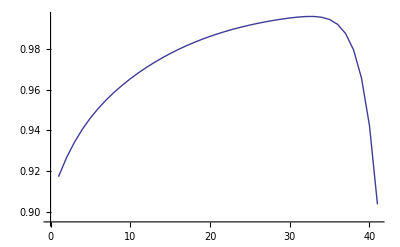

```mathematica
ListLinePlot[mass]
```

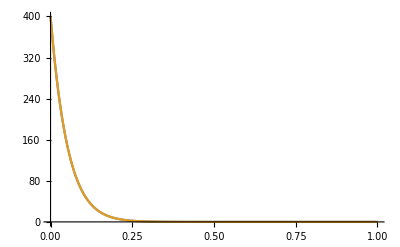

```mathematica
Plot[{D[Kimura[x,y,.1,50],x]/.x->.0,4*Entrance[y,.1,50]},{y,0,1},PlotRange->All]
```

```mathematica
?GegenbauerC
```

GegenbauerC[n,m,x] gives the Gegenbauer polynomial C_n^(m)(x). 
GegenbauerC[n,x] gives the renormalized form lim_(m→0) C_n^(m)(x)/m.

```mathematica
Clear[n]
```

```mathematica
Limit[D[4*x*(1-x)*GegenbauerC[i-1,3/2,1-2*x],x],x->0]//FullSimplify
```

2 i (1+i)

```mathematica
Entrance[y_,t_,n_:20]:=2*Sum[(2*i+1)*GegenbauerC[i-1,3/2,1-2*y]*Exp[-1/2*i*(i+1)*t],{i,1,n}]
```

```mathematica
stuff = Table[NIntegrate[Binomial[5,k]*y^k(1-y)^(5-k)*Entrance[y,.2,50],{y,0,1}],{k,0,5}]
```

{6.75839,2.49488,0.812877,0.222196,0.0461631,0.00562481}

```mathematica
stuff/Total[stuff]
```

{0.412487,0.267168,0.16358,0.0924888,0.0461478,0.0181288}

```mathematica
stuff[[2;;5]]/Total[stuff[[2;;5]]]
```

{0.907103,0.0862273,0.00634792,0.000322154}

```mathematica
Plot[Integrate[Entrance[y,t,50],{y,0,1}],{t,.001,.5},PlotRange->All]
```

-Graphics-

```mathematica
Clear[n]
```